## ListPlot examples

To plot a function, you use Plot.  To plot a collection of points, you use ListPlot.

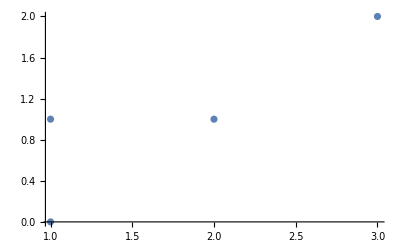

```mathematica
list = {{1,0}, {1,1}, {2,1}, {3,2}};
ListPlot[list]
```

Here are examples of plotting all of the points given by (A^k)X, where A is a 2x2 matrix, and X is an initial point in the xy plane.  We will let “mat” be our matrix, and we will obtain a list of points by using the Table command.  By plugging this into the ListPlot command, we can get a graph of the points of the form A^k X.  

(Note that in order to switch back and forth between row/column matrices, I am using the Transpose command, along with the fact that (AB)^T = B^T A^T.)

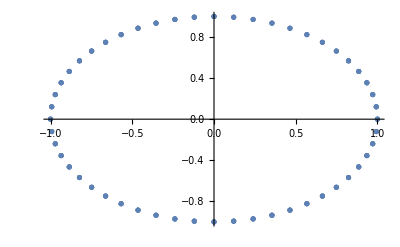

```mathematica
mat = N[({{Cos[2Pi*(1/52)], -Sin[2Pi(1/52)]}, {Sin[2Pi(1/52)], Cos[2Pi(1/52)]}})];

ListPlot[Table[ {0,1}.Transpose[MatrixPower[mat,k]], {k, 0, 200} ]]
```

By combining the above with the Manipulate command, we can get a nice picture showing us how a point evolves along progressive iterations along with how things change as the initial point changes.

```mathematica
mat1 = N[({{Cos[2Pi*(1/52)], -Sin[2Pi(1/52)]}, {Sin[2Pi(1/52)], Cos[2Pi(1/52)]}})];

Manipulate[
ListPlot[Table[ x.Transpose[MatrixPower[mat1,k]], {k, 0, n} ], PlotRange -> {{-1.2, 1.2},{-1.2, 1.2}}], 
{{n,0, "Number of iterations"}, 0, 100, 1,Appearance -> "Labeled"}, {{x, {1,0},"Initial Point"}, -1, 1, ControlType -> Slider2D, Appearance -> "Labeled"} ]
```

Here’s another example, but the matrix has been changed slightly.

```mathematica
mat2 = N[({{Cos[.1], -Sin[.1]}, {Sin[.1], Cos[.1]}})];

Manipulate[
ListPlot[Table[ x.Transpose[MatrixPower[mat2,k]], {k, 0, n} ], PlotRange -> {{-1.2, 1.2},{-1.2, 1.2}}], 
{{n,0, "Number of iterations"}, 0, 400, 1,Appearance -> "Labeled"}, {{x, {1,0},"Initial Point"}, -1, 1, ControlType -> Slider2D, Appearance -> "Labeled"} ]
```

Here is a visualization of the example we did at the beginning of class, where the linear transformation satisfied 
T(2,1) = 2(2,1) and T(0,1) = .5 (0,1).

```mathematica
mat3 = N[({{2, 0}, {3/4, 1/2}})];

Manipulate[
ListPlot[Table[ x.Transpose[MatrixPower[mat3,k]], {k, 0, n} ], PlotRange -> {{-10, 10},{-5, 5}}], 
{{n,0, "Number of iterations"}, 0, 20, 1, Appearance -> "Labeled"}, {{x, {0,1},"Initial Point"}, -1, 1, ControlType -> Slider2D, Appearance -> "Labeled"} ]
```